## Nonlinear fit

{{0.02,0.2300.020},{0.05,0.4200.020},{0.1,0.5700.020},{0.2,0.8000.010}}

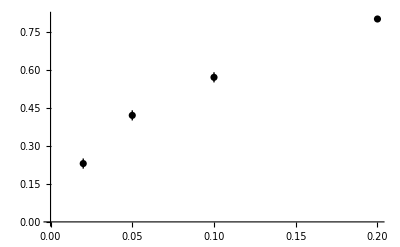

```mathematica
data={{0.02,0.23},{0.05,0.42},{0.1,0.57},{0.2,0.8}};
errors={0.02,0.02,0.02,0.01};
plotData=Table[{data[[i,1]],Around[data[[i,2]],errors[[i]]]},{i,1,Length[data]}]

p1=ListPlot[plotData,PlotStyle->Black]
```

```mathematica
model=NonlinearModelFit[data,b x^a,{a,b},x,Weights->1/errors^2,ConfidenceLevel->0.68];
model[{"BestFit","ParameterTable"}]

mid[x_]:=model[x];
high1s[x_]:=model["MeanPredictionBands"][[2]];
low1s[x_]:=model["MeanPredictionBands"][[1]];

model2s=NonlinearModelFit[data,b x^a,{a,b},x,Weights->1/errors^2,ConfidenceLevel->0.95];
high2s[x_]:=model2s["MeanPredictionBands"][[2]];
low2s[x_]:=model2s["MeanPredictionBands"][[1]];
```

{1.79837 x^0.50212, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.50212 | 0.0261245 | 19.2203 | 0.00269601
b | 1.79837 | 0.0873457 | 20.5891 | 0.00235068}

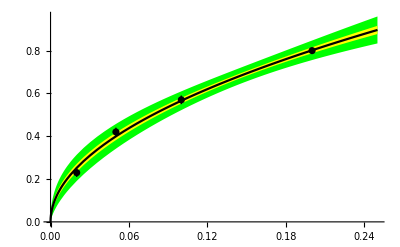

```mathematica
p2=Plot[{mid[x],high[x],low[x]},{x,0,0.25},PlotStyle->{Black,None,None},Filling->{2->{3}},FillingStyle->{Opacity[1,Yellow]}];
p3=Plot[{high2s[x],low2s[x]},{x,0,0.25},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->Opacity[1,Green]];
Show[p3,p2,p1]
```

## Linear fit

```mathematica
data={{0.02,0.23},{0.05,0.42},{0.1,0.57},{0.2,0.8}};
errors={0.02,0.02,0.02,0.01};
plotData=Table[{data[[i,1]],Around[data[[i,2]],errors[[i]]]},{i,1,Length[data]}]

fitData=Log[data]
fitErrors=errors/Table[data[[i,2]],{i,1,Length[data]}];
plotFitData=Table[{fitData[[i,1]],Around[fitData[[i,2]],fitErrors[[i]]]},{i,1,Length[fitData]}];
```

{{0.02,0.2300.020},{0.05,0.4200.020},{0.1,0.5700.020},{0.2,0.8000.010}}

{{-3.91202,-1.46968},{-2.99573,-0.867501},{-2.30259,-0.562119},{-1.60944,-0.223144}}

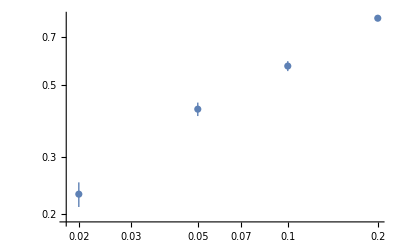

```mathematica
ListLogLogPlot[plotData]
```

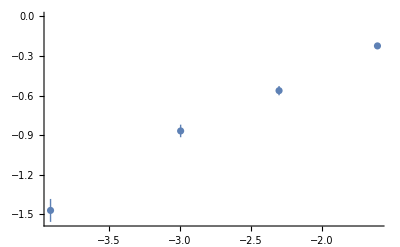

```mathematica
ListPlot[plotFitData]
```

```mathematica
lModel=LinearModelFit[fitData,x,x,Weights->1/fitErrors^2]
```

FittedModel[0.581086+0.498651 x]

```mathematica
lModel["BestFitParameters"]
```

{0.581086,0.498651}